```mathematica
R=-((D[ν[r],r])^2*r^2-D[ν[r],r]*D[u[r],r]*r^2+2*D[ν[r],{r,2}]*r^2+4*r*D[ν[r],r]-4*r*D[u[r],r]-4*Exp[u[r]]+4)/(2*r^2*Exp[u[r]])
```

1/(2 r^2)ⅇ^(-u[r]) (-4+4 ⅇ^u[r]+4 r u'[r]-4 r ν'[r]+r^2 u'[r] ν'[r]-r^2 ν'[r]^2-2 r^2 ν''[r])

```mathematica
detg=-Exp[ν[r]]*Exp[u[r]]*r^4
```

-ⅇ^(u[r]+ν[r]) r^4

```mathematica
PowerExpand[Sqrt[-detg]]
```

ⅇ^(1/2 (u[r]+ν[r])) r^2

```mathematica
L=Simplify[R*ⅇ^(1/2 (u[r]+ν[r])) r^2]
```

1/2 ⅇ^(1/2 (-u[r]+ν[r])) (-4+4 ⅇ^u[r]-4 r ν'[r]-r^2 ν'[r]^2+r u'[r] (4+r ν'[r])-2 r^2 ν''[r])

```mathematica
eq01=Simplify[D[L,ν[r]]-D[D[L,ν'[r]],r]+D[D[L,ν''[r]],{r,2}]]==0
```

ⅇ^(1/2 (-u[r]+ν[r])) (-1+ⅇ^u[r]+r u'[r])==0

```mathematica
eq01=Simplify[D[L,u[r]]-D[D[L,u'[r]],r]+D[D[L,u''[r]],{r,2}]]==0
```

ⅇ^(1/2 (-u[r]+ν[r])) (-1+ⅇ^u[r]-r ν'[r])==0

```mathematica
Simplify[L+ ⅇ^(1/2 (-u[r]+ν[r])) r^2 ν''[r]]
```

1/2 ⅇ^(1/2 (-u[r]+ν[r])) (-4+4 ⅇ^u[r]-4 r ν'[r]-r^2 ν'[r]^2+r u'[r] (4+r ν'[r]))

```mathematica
Lred=Simplify[L+ ⅇ^(1/2 (-u[r]+ν[r])) r^2 ν''[r]+D[ⅇ^(1/2 (-u[r]+ν[r]))*r^2,r]*D[ν[r],r]]
```

2 ⅇ^(1/2 (-u[r]+ν[r])) (-1+ⅇ^u[r]+r u'[r])

```mathematica
eq1=D[Lred,ν[r]]-D[D[Lred,ν'[r]],r]==0
```

ⅇ^(1/2 (-u[r]+ν[r])) (-1+ⅇ^u[r]+r u'[r])==0

```mathematica
eq2=D[Lred,u[r]]-D[D[Lred,u'[r]],r]==0
```

-2 ⅇ^(1/2 (-u[r]+ν[r]))+2 ⅇ^(u[r]+1/2 (-u[r]+ν[r]))-ⅇ^(1/2 (-u[r]+ν[r])) (-1+ⅇ^u[r]+r u'[r])-ⅇ^(1/2 (-u[r]+ν[r])) r (-u'[r]+ν'[r])==0

```mathematica
Simplify[eq2]
```

ⅇ^(1/2 (-u[r]+ν[r])) (-1+ⅇ^u[r]-r ν'[r])==0

```mathematica
DSolve[{eq2,eq1},{ν[r],u[r]},r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u[r]→Log[1/2 (1-Tanh[1/2 (C[1]-Log[r])])],ν[r]→C[2]-Log[r]/2+Log[Cosh[1/2 (-C[1]+Log[r])]]}}

```mathematica
Limit[Log[1/2 (1-Tanh[1/2 (C[1]-Log[r])])],r-> Infinity]
```

0

```mathematica
Limit[C[2]-Log[r]/2+Log[Cosh[1/2 (-C[1]+Log[r])]],r->Infinity]
```

C[2]+Log[ⅇ^(-C[1]/2)/2]

```mathematica
u[r_]=Log[1/2 (1-Tanh[1/2 (-Log[r])])]
```

Log[1/2 (1+Tanh[Log[r]/2])]

```mathematica
ν[r_]=-Log[r]/2+Log[Cosh[1/2 (2*Log[2]+Log[r])]]
```

-Log[r]/2+Log[Cosh[1/2 (2 Log[2]+Log[r])]]

```mathematica
Limit[ν[r],r-> Infinity]
```

0

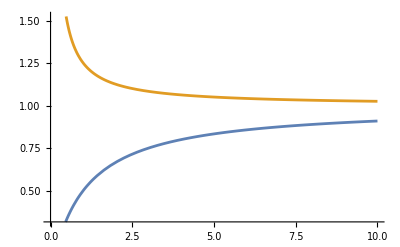

```mathematica
Plot[{Exp[u[r]],Exp[ν[r]]},{r,0,10}]
```

```mathematica
Exp[u[r]]
```

1/2 (1+Tanh[Log[r]/2])

```mathematica
Exp[ν[r]]
```

Cosh[1/2 (2 Log[2]+Log[r])]/(√r)

```mathematica
DSolve[D[Exp[-λ[r]]*r,r]==1,λ[r],r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{λ[r]→Log[1/2 (1-Tanh[1/2 (C[1]-Log[r])])]}}